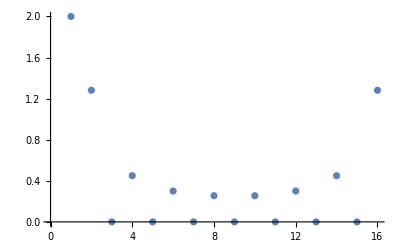

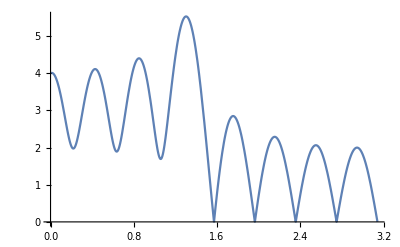

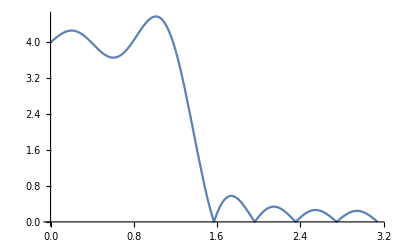

```mathematica
filtr={1,1,1,1,0,0,0,0};
filtrOK=Join[filtr,Reverse[filtr]];
fourier=Fourier[filtrOK];
ListPlot[Abs@fourier]
Plot[Abs@ListFourierSequenceTransform[fourier,ω],{ω,0,π}]
Plot[Abs@ListFourierSequenceTransform[RotateLeft[fourier,(Length@fourier)/2],ω],{ω,0,π}]
```

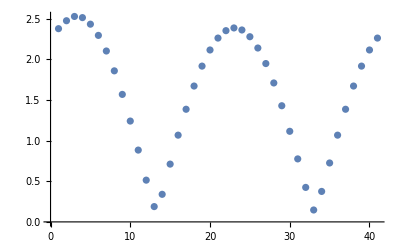

```mathematica
f=1;
fp=40;
data=Table[Cos[2π f t],{t,0,1,1/fp}];
ListPlot@Abs@ListConvolve[fourier,data,1]
```